# CoP in the XY Model

```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Import[NotebookDirectory[]<>"/GaussianOptimization.m"]
```

#### Covariance matrix of ground state of the XY model

```mathematica
Clear[XYft,XYcm,XYcmRes]
XYft[{L_,J_,h_,γ_}]:=XYft[{L,J,h,γ}]=Module[{ϵ,a,b,u,v,cor,part1,part2},
u[0]=0;v[0]=ⅈ;u[π]=1;v[π]=0; (* This is no really needed for even number of excitations, but would be relevant, if we were to construct eigenstates with odd number of excitations! *)
ϵ[k_]:=ϵ[k]=√(h^2+2h J Cos[k]+J^2+(γ^2-1)J^2 Sin[k]^2);
a[k_]:=a[k]=-J Cos[k]-h;
b[k_]:=b[k]=γ J Sin[k];
u[k_]:=u[k]=(ϵ[k]+a[k])/(√(2ϵ[k](ϵ[k]+a[k])));
v[k_]:=v[k]=(ⅈ b[k])/(√(2ϵ[k](ϵ[k]+a[k])));
cor=Table[ⅇ^(ⅈ π (x+1)/L),{x,0,L-1}]//N;
part1=((Table[1/(√L)(Abs[v[(2π k+π)/L]]^2-Abs[u[(2π k+π)/L]]^2//N)ⅇ^(ⅈ 2π k/L),{k,0,L-1}]//Fourier)*cor)//Re;
part2=(((Table[1/(√L)2Im[v[(2π k+π)/L]u[(2π k+π)/L]] ⅇ^(ⅈ 2π k/L),{k,0,L-1}]//Fourier)*cor)//Im);
part1+part2]

XYcm[var_]:=XYcm[var]=Module[{L,ft,ΩBlock},
L=var⟦1⟧;
ft=XYft[var];
ΩBlock=ToeplitzMatrix[ReplacePart[RotateRight[ft,1],1->-Last[ft]],-Reverse[ft]];
ArrayFlatten[{{0.,ΩBlock},{-Transpose[ΩBlock],0.}}]
](* in qqpp basis *)
XYcmRes[var_,{dimA_,dimB_,d_}]:=Module[{L,ind,ΩRes},
L=var⟦1⟧;
ind=Join[Table[i,{i,dimA}],Table[i+dimA+d,{i,dimB}]];
ΩRes=Table[If[Mod[j-l,L]==0,-Reverse[XYft[var]]⟦1⟧,Sign[j-l]XYft[var]⟦Mod[j-l,L]⟧],{j,ind},{l,ind}];
GOqpqpFROMqqpp[dimA+dimB].ArrayFlatten[{{0.,ΩRes},{-Transpose[ΩRes],0.}}].Transpose[GOqpqpFROMqqpp[dimA+dimB]]
] (* in qpqp basis *)
```

## Fermionic Complexity of Purification (CoP)

```mathematica
L=100; (* Total number lattice sites *)
J=2.5;h=2;γ=1; (* XY model parameter*)
dimA1=1; dimB1=3; (* dofs of chosen subystems *)
d=5; (* distance subsystems *)
dimPur=dimA1+dimB1; (* dimensions of the purifying system*)
```

### Pre-algorithm: Create complex structures and initial transformations

```mathematica
CM0=XYcmRes[{L,J,h,γ},{dimA1,dimB1,d}];
{rlist,MTra}=GOExtractStdFormΩ[CM0];

JT=GOPurifyStandardJFermion[rlist,dimPur,"qpqp"];
JR=GOTransformΩtoJ[GOΩqpqp[dimA1+dimB1+dimPur],"qpqp","qpqp"]; (* reference state *)

J0=JR;
M0=ArrayFlatten[{{MTra,0},{0,IdentityMatrix[2dimPur]}}]//SparseArray; (* Attention: For complexity, we need to put MTra, because JR transforms inversely to JT!!! *)
```

### 1. Define the problem-specific input arguments

```mathematica
function=GOCoPFerm[JT]; gradient=GOCoPgradFerm[JT];
ProblemSpecific={function,gradient};
```

### 2. Define the system-specific input arguments

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSONoUN[dimPur]}];
M0List=Table[MatrixExp[RandomReal[{0,0.7},Length[LieBasis]].LieBasis].M0,{i,10}];
geometry=GOGeometryConst[LieBasis,J0,-1];
newM[m_,s_,x_]:=m.GOapproxExp[s,x];
```

```mathematica
SystemSpecific={J0,M0List,LieBasis,geometry,newM};
```

### 3. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-8; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

### Run the Optimization and evaluate results

```mathematica
{time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

Reason for termination: Function value tolerance reached

Time taken: 46.3718 seconds

Final value: 1.0434

Number of iterations: 764

Number of total corrections: 0

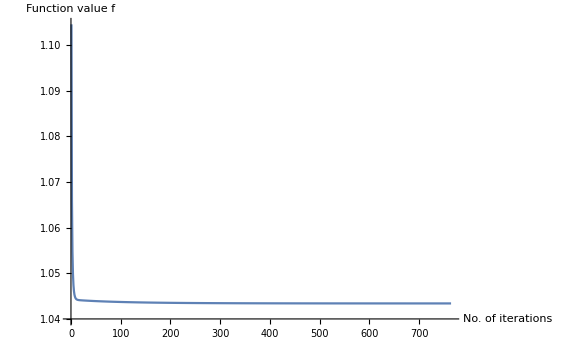

```mathematica
Print["Reason for termination: ",Result[[7]]];
Print["Time taken: ",time," seconds"];
Print["Final value: ",Result⟦1,1⟧];
Print["Number of iterations: ",Length[Result⟦4,1⟧]];
Print["Number of total corrections: ",Result⟦3⟧//Total];
ListPlot[Result⟦5⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All,Joined->True]
```